Function description:
1. This executable read  “savedata_config”, and then read residual in .dta files and a f(x,Q) data file to calculate observables, saving data of observables into /PDFDataDir/PDFDataFile
2. (x, Q) are points of  grid method (please read the tutorial note of this program)
3. – arguments that users should setup

∗ PDF set Dir, PDF method, Expt ID List, datalis file

∗ Correlation Path & Correlation File



∗ F(x,Q) Grid Path & F(x,Q) Grid File, Nx, NQ for grid f(x,Q) data

– output: if Path & File are “default”, the program make files with all $obs indexes:

– ./quick_data/{$obs}_samept_data_{$PDFname}_x{$Nx}_{$NQ}.m, where $PDFname = PDFname, ex: CT14NNLO, $obs = “corr”, ”dRcorr”, ”dR”, ”residual”, ”residualNset”, ”expterror”

data in the file is a List of dimension: 
“corr”: [[iexpt, iflavour]]
“dRcorr”: [[iexpt, iflavour]]
“ dR”: [[iexpt, iflavour]]
“residual”: [[iexpt, iflavour]]
“residualNset”: [[iexpt, iflavour]]
“expterror”: [[iexpt, iflavour]]

```mathematica
SetDirectory[NotebookDirectory[](*DirectoryName[$InputFileName]*) ]
Get["corr_proj_funcs.m"]
```

/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin

```mathematica
DtaExptList[dtaDirin_]:=
Module[{dtaDir=dtaDirin,dtafile,dtadata,exptlist},
dtafile=FileNames[dtaDir<>"*dta"][[1]];
(*assume the data in .dta file is "ct2016 format"*)
dtadata=ReadExptTable[dtafile,"ct2016"];
exptlist=Table[dtadata[[iexpt,1]],{iexpt,1,Length[dtadata]}];
exptlist
]
```

```mathematica
readsavedataconfigfile[configDirin_,configfilenamein_]:=
Module[{configDir=configDirin,configfilename=configfilenamein,
PDFsetDirTag,PDFsetmethodTag,ExptIDListTag,datalistFileTag,FxQGridDirTag,FxQSameptDirTag,CorrDataDirTag,GridNxTag,GridNQTag,
PDFsetDir,PDFsetmethod,ExptIDList,datalistFile,FxQGridDir,FxQSameptDir,CorrDataDir,GridNx,GridNQ,
itag,s,output,output2,output3
},


PDFsetDirTag="PDF set Dir";
PDFsetmethodTag="PDF method";
ExptIDListTag="Expt ID List";
datalistFileTag="datalis file";
FxQGridDirTag="F(x,Q) Grid Path";
FxQSameptDirTag="F(x,Q) Samept Path";
CorrDataDirTag="Correlation Path";

GridNxTag="Nx";
GridNQTag="NQ";
{PDFsetDirTag,PDFsetmethodTag,ExptIDListTag,datalistFileTag,FxQGridDirTag,FxQSameptDirTag,CorrDataDirTag,GridNxTag,GridNQTag};

PDFsetDir="unset";
PDFsetmethod="unset";
ExptIDList="unset";
datalistFile="unset";
FxQGridDir="unset";
FxQSameptDir="unset";
CorrDataDir="unset";

GridNx="unset";
GridNQ="unset";
{PDFsetDir,PDFsetmethod,ExptIDList,datalistFile,FxQGridDir,FxQSameptDir,CorrDataDir,GridNx,GridNQ};


(*read config file line by line into list*)
s=OpenRead[configDir<>configfilename];
output=ReadList[s,String];
Close[s];

(*delete comments: with "#" at begining of line*)
output2={};
Table[
If[StringTake[output[[i]],1]≠"#",output2=Append[output2,output[[i]] ] ];
"dummy"
,{i,1,Length[output]}
];
(*seperate the tag of configure file and arguments by ":"*)
output3=Table[StringSplit[output2[[i]],":"],{i,1,Length[output2]}];

{PDFsetDirTag,PDFsetmethodTag,ExptIDListTag,datalistFileTag,FxQGridDirTag,FxQSameptDirTag,CorrDataDirTag};
(*check tag exist, if a tag exist, read arguments corresponding to that tag*)
(*read PDFset Dir*)
itag=1;
If[output3[[itag,1]]==PDFsetDirTag,PDFsetDir=output3[[itag,2]];PDFsetDir=Read[StringToStream[PDFsetDir],Word] ];

(*read PDF method *)
itag=itag+1;
If[output3[[itag,1]]==PDFsetmethodTag,PDFsetmethod=output3[[itag,2]];PDFsetmethod=Read[StringToStream[PDFsetmethod],Word] ];

(*read ExptID List *)
itag=itag+1;
If[output3[[itag,1]]==ExptIDListTag,ExptIDList=output3[[itag,2]];ExptIDList=ReadList[StringToStream[ExptIDList],Number] ];

(*read datalist File *)
itag=itag+1;
If[output3[[itag,1]]==datalistFileTag,datalistFile=output3[[itag,2]];datalistFile=Read[StringToStream[datalistFile],Word] ];

(*read FxQGrid Dir *)
itag=itag+1;
If[output3[[itag,1]]==FxQGridDirTag,FxQGridDir=output3[[itag,2]];FxQGridDir=Read[StringToStream[FxQGridDir],Word] ];

(*read FxQSamept Dir *)
itag=itag+1;
If[output3[[itag,1]]==FxQSameptDirTag,FxQSameptDir=output3[[itag,2]];FxQSameptDir=Read[StringToStream[FxQSameptDir],Word] ];

(*read Correlation Data Dir *)
itag=itag+1;
If[output3[[itag,1]]==CorrDataDirTag,CorrDataDir=output3[[itag,2]];CorrDataDir=Read[StringToStream[CorrDataDir],Word] ];

(*read Grid Nx *)
itag=itag+1;
If[output3[[itag,1]]==GridNxTag,GridNx=output3[[itag,2]];GridNx=Read[StringToStream[GridNx],Number] ];

(*read Grid NQ *)
itag=itag+1;
If[output3[[itag,1]]==GridNQTag,GridNQ=output3[[itag,2]];GridNQ=Read[StringToStream[GridNQ],Number] ];


{PDFsetDir,PDFsetmethod,ExptIDList,datalistFile,FxQGridDir,FxQSameptDir,CorrDataDir,GridNx,GridNQ}
]
```

## Implement

### set input arguments

```mathematica
(*set input arguments *)

configDir=NotebookDirectory[];(*DirectoryName[$InputFileName];*)
(*configfilename="config_pdf_resolution_test.txt";*)
configfilename="savedata_config.txt";
```

```mathematica
(*read arguments from config file*)
{PDFsetDir,PDFsetmethod,ExptIDList,datalistFile,FxQGridDir,FxQGridFile,(*FxQSameptDir*)dummy2,(*FxQSameptFile*)dummy3,CorrDataDir,CorrDataFile,GridNx,GridNQ}=
readsavedataconfigfile[configDir,configfilename]
```

{/home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/,Hessian,{566,568},dat17lisformathematica,default,fxQ_grid_2017.0425.2123.-0500_ct14nn-new_x80_Q25.m,default,default,default,default,80,25}

```mathematica
myPDFsetDir=PDFsetDir

myPDFsetdtafile=FileNames[myPDFsetDir<>"*dta"][[1]];
(*set PDFset*)
PDFname=StringSplit[myPDFsetDir,"/"][[-1]]

(*set dta Dir you want to read data, it's the PDFset Dir you choose*)
DtaDir=myPDFsetDir;
```

/home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/

2017.0604.1856.-0500_CT14-2_mod

```mathematica
(*if path setting is default, set it as in quick_data directory*)
quickdataDir="../quick_data/";
If[datalistFile=="default",datalistFile="./dat16lisformathematica"]
If[FxQGridDir=="default",FxQGridDir=quickdataDir]
If[FxQGridFile=="default",FxQGridFile="fxQ_grid_"<>PDFname<>"_x"<>ToString[GridNx]<>"_Q"<>ToString[GridNQ]<>".m"]
(*
If[FxQSameptDir=="default",FxQSameptDir=quickdataDir]
If[FxQSameptFile=="default",FxQSameptFile=]
*)
If[CorrDataDir=="default",CorrDataDir=quickdataDir]
If[CorrDataFile=="default",CorrDataFile="grid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>"_Q"<>ToString[GridNQ]<>".m"]
```

../quick_data/

../quick_data/

grid_data_2017.0604.1856.-0500_CT14-2_mod_x80_Q25.m

```mathematica
Directory[]
```

/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin

```mathematica
ReadLisFile[datalistFile]
```

{{101,BcdF2pCor},{102,BcdF2dCor},{103,NmcF2pCor},{104,NmcRatCor},{105,NmcF2rX},{106,NmcX0pCor},{115,BcdX0pCor},{116,BcdX0dCor},{108,cdhswf2},{109,cdhswf3},{110,ccfrf2.mi},{111,ccfrf3.md},{122,ChorusNuX0},{123,ChorusNbX0},{124,NuTvNuChXN},{125,NuTvNbChXN},{126,CcfrNuChXN},{127,CcfrNbChXN},{140,Hn+9697f2c},{143,Hn+9900x0c},{145,Hn+9900x0b},{146,Hn0407f2c},{147,Hn1X0c},{156,Zn+9697f2c},{157,Zn+9800f2c},{159,HERA1X0},{160,HERAIpII},{164,e140Rd},{165,e143RC},{166,H1FL00},{167,H1FL03a},{168,H1FL03b},{169,H1FL10},{170,EMCF2c},{171,EMCX0c},{180,epFLbench},{181,epF1bench},{182,epF2bench},{183,epF3bench},{184,emFLbench},{185,emF1bench},{186,emF2bench},{187,emF3bench},{201,e605},{203,e866f},{204,e866ppxf},{205,e866pdxf},{221,cdfWprod},{225,cdfLasy},{227,cdfLasy2},{231,d02Easy1},{232,d02Easy2},{233,d02Easy3},{234,d02Masy1},{235,d02Masy2},{236,d02Masy3},{240,LHCb7_WZ1},{241,LHCb7Wasy1},{242,LHCb7Wasy2},{243,LHCb7Wasy3},{244,LHCb7Wa1N},{245,LHCb7ZWrap},{246,LHCb8Zeer},{247,ATL7Zpt},{248,ATL7ZW},{249,CMS8Wxa},{250,LHCb8WZ},{260,ZyD02a},{261,ZyCDF2},{265,CMS7Masy1},{266,CMS7Masy2},{267,CMS7Easy},{268,ATL7_WZ},{275,ATL7DYhm},{276,ATL7DYlm},{277,ATL7DYext},{281,d02Easy5},{283,d02EasyI},{284,d02EasyII},{285,d02EasyIII},{286,d02EasyIV},{299,ATL13_WZ},{401,ttbTeV2},{402,ttbLHC7},{403,ttbLHC8},{404,ttbLHC14},{405,ttbLHC13},{504,cdf2jtCor2},{505,cdf1jtCorB},{506,cdf1jtCorB},{514,d02jtCor2},{515,d01Bjet},{517,d01Bjet},{518,d02dijet},{534,ATL7jtR4},{535,ATL7jtR6},{536,ATL7dijtR4},{537,ATL7dijtR6},{538,CMS7jtR7v2},{542,CMS7jtR7y6},{543,ATL7jtR4u},{544,ATL7jtR6u},{551,ATLratR4},{552,ATLratR6},{561,CMS8ttbpt},{562,CMS8ttbya},{563,CMS8ttbmtt},{564,CMS8ttbytt},{565,ATL8ttbpt},{566,ATL8ttbya},{567,ATL8ttbmtt},{568,ATL8ttbytt},{601,ptE288},{602,ptE605},{603,ptCDFz1},{604,ptD0z1},{605,ptR209},{606,ptD0z2},{607,ptCDFz2},{701,fkH0a7},{702,fkH0a8},{703,fkH0a14},{704,fkWp},{705,fkWm},{706,fkZ0},{707,fkH0a13},{708,fkZ0pr},{709,fkWppr},{710,fkWmpr}}

```mathematica
exptlist=ExptIDList;
Print["read data expt id: ",exptlist];
```

read data expt id: {566,568}

### read f(x, Q) grid from FxQGridDir file

```mathematica
Directory[]
FxQGridDir
```

/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin

../quick_data/

```mathematica
(*set the save path*)
(*quickdataDir="../quick_data/";*)
(*
NQ=GridNQ;Nx=GridNx;
fxQfile="fxQ_grid_"<>PDFname<>"_x"<>ToString[Nx]<>"_Q"<>ToString[NQ]<>".m";
*)
```

```mathematica
fxQgrid2class=Import[FxQGridDir<>FxQGridFile,"ExpressionML"];
```

```mathematica
Dimensions[fxQgrid2class]
fxQgrid2class[[1]][["data"]][[1]]
```

{11}

LF[0.00001,2.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.]

```mathematica
Dimensions[fxQgrid2class][[1]]
fxQgrid2class[[1]][["data"]][[1]]
```

11

LF[0.00001,2.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.]

```mathematica
(*add customized flavour for parton density function (flavour = 6,7,8)*)

fxQgrid2class=Join[fxQgrid2class,setextrafxQ[fxQgrid2class]  ]
```

{<|label→{x,Q,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56},data→{1},PDFinfo→<|PDFname→2017.0425.2123.-0500_ct14nn-new,PDFsetmethod→Hessian,Nset→57,iset→unset,flavour→-5|>|>,12,<|1|>}
 |  |  |  |

```mathematica
Dimensions[fxQgrid2class][[1]]
fxQgrid2class[[1]][["data"]][[1]]
```

14

LF[0.00001,2.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.]

### read .dta files

```mathematica
(*read expt data from .dta files*)
exptdata=Readdtafile[["readdta"]][DtaDir,exptlist]
```

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.00.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.01.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.02.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.03.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.04.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.05.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.06.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.07.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.08.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.09.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.10.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.11.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.12.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.13.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.14.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.15.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.16.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.17.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.18.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.19.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.20.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.21.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.22.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.23.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.24.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.25.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.26.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.27.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.28.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.29.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.30.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.31.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.32.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.33.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.34.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.35.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.36.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.37.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.38.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.39.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.40.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.41.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.42.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.43.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.44.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.45.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.46.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.47.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.48.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.49.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.50.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.51.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.52.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.53.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.54.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.55.dta

50 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/2017.0604.1856.-0500_CT14-2_mod/If1350.56.dta

find exptid = 566.

find exptid = 568.

{{{566,ATL8ttbya,5,2.41736},{566,ATL8ttbya,5,2.55637},{566,ATL8ttbya,5,2.46972},{566,ATL8ttbya,    Pt         Ymn      Ymx          Exp     …   ShiftedData  UnCorErr  ReducedChi2  lob/lio,1.,5,…,{dtaread2016boting`Private`LF[0.,0.,0.2,182.53,169.81,19.17,1.075,0.113,-0.44,12.17,170.4,1.117,-0.25,0],3,dtaread2016boting`Private`LF[0.,1.4,2.,39.108,39.0182,4.595,1.002,0.118,0.,0.4587,38.65,0.5025,0.54,0]},2.57626},49,{1},{566,ATL8ttbya,5,2.42186},{566,ATL8ttbya,5,2.51612},{566,ATL8ttbya,5,2.21887}},1}
 |  |  |  |

```mathematica
Dimensions[exptdata]
```

{2,57,8}

### transform .dta data into dtadataclass

```mathematica
(*for all data read from .dta files, transf them to dtadata class*)
mydtadata=
Table[
Readdtafile[["toclass"]][exptdata[[iexpt,iset]],PDFname,PDFsetmethod],
(*todtadataclass[exptdata[[i,j]],PDFname,PDFsetmethod],*)
{iexpt,1,Dimensions[exptdata][[1]]},{iset,1,Dimensions[exptdata][[2]]}
]
```

{{<|label→{wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat},data→{dtaread2016boting`Private`LF[0.,0.,0.2,182.53,169.775,19.17,1.075,0.113,-0.443,12.25,170.3,1.117,-0.2,0],3,dtaread2016boting`Private`LF[0.,1.4,2.,39.108,38.8126,4.595,1.008,0.118,-0.004,0.6225,38.49,0.5025,0.42,0]},exptinfo→<|1|>,PDFinfo→<|PDFname→2017.0604.1856.-0500_CT14-2_mod,4|>,rawdata→{566,ATL8ttbya,4,2.41736}|>,55,<|1|>},1}
 |  |  |  |

```mathematica
Dimensions[mydtadata]
mydtadata[[2,1]];
```

{2,57}

### add {x,Q} to data label

```mathematica
(*if samept, run it, otherwise only transf data structure into LF[...]*)
(*add transformed {x,Q} in dtadata*)
(*x, Q will be the column 14, 15 in a data*)


(*decide calculate the grid correlation or samept correlation*)
fxQmode="grid";
If[
fxQmode=="samept",
Table[
(*add data by formula*)
mydtadata[[iexpt,iset]][["data"]]=selectExptxQv2[mydtadata[[iexpt,iset]][["exptinfo","exptid"]],mydtadata[[iexpt,iset]][["data"]],"dummy"];
(*add label of {x,Q} to -2&-1 -th column*)
mydtadata[[iexpt,iset]][["label"]]=Join[mydtadata[[iexpt,iset]][["label"]],{"x","Q"}];
(*LF[...] become global*)
mydtadata[[iexpt,iset]]=Datamethods[["LFglobal"]][mydtadata[[iexpt,iset]] ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
]
];

If[
fxQmode=="grid",
Table[
mydtadata[[iexpt,iset]]=Datamethods[["LFglobal"]][mydtadata[[iexpt,iset]] ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
]
];
```

```mathematica
mydtadata[[1,1]][["label"]]
Datamethods[["getNcolumn"]][mydtadata[[1,1]] ]
Take[mydtadata[[1,1]][["data"]],3]
```

{wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat}

14

{LF[0.,0.,0.2,182.53,169.775,19.17,1.075,0.113,-0.443,12.25,170.3,1.117,-0.2,0],LF[0.,0.2,0.6,165.78,154.263,17.65,1.075,0.114,-0.426,9.775,156.,0.9798,-3.16,0],LF[0.,0.6,1.,131.36,126.195,14.33,1.041,0.114,-0.13,6.579,124.8,0.9602,2.17,0]}

```mathematica
(*potential problem of read .dta file: since some exptid will not in data file, mydata will lose these data and exptid of exptlist is different  with mydata*)
Dimensions[mydtadata]
```

{2,57}

```mathematica
mydtadata[[1,1]];
```

### set a class with data struture LF[x,Q,residual]

```mathematica
mydtadata[[1,1]][["label"]]
mydtadata[[2,1]][["label"]]
mydtadata[[3,1]][["label"]]
```

{wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat}

{wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat}

Part::partw: Part 3 of {{«1»,<|label→{wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat},«3»,rawdata→{566,ATL8ttbya,«4»,2.55637}|>,«47»,<|label→{wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat},«3»,rawdata→{566,ATL8ttbya,«4»,2.41453}|>,«7»},{«1»}} does not exist.

Part::pspec1: Part specification label is not applicable.

Part::partw: Part 3 of {{«1»,<|label→{wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat},«3»,rawdata→{566,ATL8ttbya,«4»,2.55637}|>,«47»,<|label→{wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat},«3»,rawdata→{566,ATL8ttbya,«4»,2.41453}|>,«7»},{«1»}} does not exist.

Part::pspec1: Part specification label is not applicable.

{{<|label→{wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat},3,rawdata→{566,ATL8ttbya,4,2.41736}|>,55,<|label→{wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat,wrongformat},3,rawdata→{566,ATL8ttbya,4,2.21887}|>},{1}}⟦3,1⟧⟦label⟧
 |  |  |  |

```mathematica
Table[
mydtadata[[iexpt,iset]][["data"]]=mydtadata[[iexpt,iset]][["data"]]/.LF[a__]:>LF[Sequence@@{a},({a}[[5]]-{a}[[11]])/{a}[[12]] ];
mydtadata[[iexpt,iset]][["label"]]=Join[mydtadata[[iexpt,iset]][["label"]],{"residual"}];
"dummy",
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
```

```mathematica
mydtadata[[2,1]][["label"]]
mydtadata[[2,1]][["data"]];
mydtadata[[2,1]][["rawdata"]];
```

```mathematica
{"wrongformat","wrongformat","wrongformat","wrongformat","wrongformat","wrongformat","wrongformat","wrongformat","wrongformat","wrongformat","wrongformat","wrongformat","wrongformat","wrongformat","residual"}
```

```mathematica
(*extract Nset of data [[iexpt,iset,{residual},Npt]]*)
(*
dataNset=
Table[
(*grab residual*)
Datamethods[["picktolist"]][mydtadata[[iexpt,iset]],{-1} ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
*)
```

```mathematica
(*input the dataclass[[Nset]] and the columnN, extract {LF[columnN(1),...,columnN(Nset)]} *)
getNsetLF[dataclassin_,columnin_]:=
Module[{dataclass=dataclassin,column=columnin,dataNset,Nset},
Nset=Length[dataclass];
(*extract Nset of data [[iset,{residual},Npt]]*)
dataNset=
Table[
(*grab residual*)
Datamethods[["picktolist"]][dataclass[[iset]],{column} ],
{iset,1,Nset}
];

(*transf to [[Npt,{residual},Nset]] format*)
dataNset=Transpose[dataNset,{3,2,1}];


(*transf to [[Npt,Nset]] format*)
(*CT14NNLO: [[Npt]]=LF[obs0,...obs56]*)
dataNset=
Table[
(*1 represent residual index*)
dataNset[[ix,1]]/.List->LF,
{ix,1,Length[dataNset]}
];

dataNset
]
```

### for every grids, calculate LF[x,Q, Corr(residual, f(x, Q) )], then pick up only correlation close to maximum

```mathematica
Dimensions[fxQgrid2class]
```

{14}

```mathematica
(*residualNset[[iexpt,ix]] = LF[obs1,obs2,...,obs Nset]*)
residualNset=Table[getNsetLF[mydtadata[[iexpt]],-1],{iexpt,1,Length[mydtadata]}];
```

```mathematica
(*calculate dR*)
dR=Table[
pdfHessianSymErrorfake[residualNset[[iexpt,ix]]/.LF->List],
{iexpt,1,Length[residualNset]},{ix,1,Length[residualNset[[iexpt]] ]}
];
```

```mathematica
dR;
```

```mathematica
fmax=Length[fxQgrid2class]
```

14

```mathematica
(*calculate correlation of fxQgrid2class[[flavour]], residual[[iexpt,Npt]] for all grid points, then select the maximum corr data*)
(*output format [[iexpt,flavour,ix of data set]]*)
(*data of corr*)
obsgridLFdata=
Table[
(*calculate correlation of all (x, Q) grids*)
(*time1=AbsoluteTiming[*)

corrgridLF=
Table[
x=fxQgrid2class[[flavour+6]][["data"]][[igrid]][[1]];Q=fxQgrid2class[[flavour+6]][["data"]][[igrid]][[2]];
corrxQ=pdfHessianCorrelationfake[fxQgrid2class[[flavour+6]][["data"]][[igrid]]/.LF[a__]:>Drop[{a},2],residualNset[[iexpt,ix]]/.LF->List];
dRcorrxQ=dR[[iexpt,ix]]*corrxQ;
dRxQ=dR[[iexpt,ix]];
 expterrorxQ=mydtadata[[iexpt,1]][["data"]][[ix]]/.LF[a__]:>{a}[[6]]/{a}[[4]];
residualxQ=residualNset[[iexpt,ix]][[1]];
LF[x,Q,expterrorxQ,residualxQ,dRxQ,dRcorrxQ,corrxQ],
{igrid,1,Datamethods[["getNpt"]][fxQgrid2class[[flavour+6]] ]}
];

(*];*)
(*
time2=AbsoluteTiming[
(*max, min or corr*)
maxcorr=Max[corrgridLF/.LF[a__]:>{a}[[3]] ];
mincorr=Min[corrgridLF/.LF[a__]:>{a}[[3]] ];
(*pick points with correlation close to the maximum value*)
output=
If[
maxcorr>Abs[mincorr],
Select[corrgridLF,#[[3]]≥ 1.0*maxcorr&],
Select[corrgridLF,#[[3]]≤ 1.0*mincorr&]
];
];
*)
(*Print["flavour, iexpt, ix, t1, t2: ",{flavour,iexpt,ix,time1}];*)
corrgridLF
(*search only maximum corr of (x,Q,corr)*),
{iexpt,1,Length[residualNset]},{flavour,-5,fmax-6},{ix,1,Length[residualNset[[iexpt]] ]}
];

(*output format [[iexpt,flavour,ix of data set]]*)
(*data of dR*corr*)
(*
dRcorrgrid=
Table[
(*calculate correlation of all (x, Q) grids*)
time1=AbsoluteTiming[

dRcorrgridLF=
Table[
x=fxQgrid2class[[flavour+6]][["data"]][[igrid]][[1]];Q=fxQgrid2class[[flavour+6]][["data"]][[igrid]][[2]];
LF[x,Q,dR[[iexpt,ix]]*pdfHessianCorrelationfake[fxQgrid2class[[flavour+6]][["data"]][[igrid]]/.LF[a__]:>Drop[{a},2],residualNset[[iexpt,ix]]/.LF->List] ],
{igrid,1,Datamethods[["getNpt"]][fxQgrid2class[[flavour+6]] ]}
];
];

time2=AbsoluteTiming[
maxdRcorr=Max[dRcorrgridLF/.LF[a__]:>{a}[[3]] ];
mindRcorr=Min[dRcorrgridLF/.LF[a__]:>{a}[[3]] ];
(*pick points with correlation close to the maximum value*)
output=
If[
maxdRcorr>Abs[mindRcorr],
Select[dRcorrgridLF,#[[3]]≥1.0*maxcorr&],
Select[dRcorrgridLF,#[[3]]≤ 1.0*mincorr&]
];
];
output
(*search only maximum corr of (x,Q,corr)*),
{iexpt,1,Length[residualNset]},{flavour,-5,5},{ix,1,Length[residualNset[[iexpt]] ]}
];
*)
```

```mathematica
Take[obsgridLFdata[[1,6,12]],3]
```

Part::partw: Part 12 of «1» does not exist.

1
 |  |  |  |

```mathematica
(*
Table[
(*max, min or corr*)
maxcorr=Max[obsgridLFdata[[iexpt,flavour+6,ix]]/.LF[a__]:>{a}[[6]] ];
mincorr=Min[obsgridLFdata[[iexpt,flavour+6,ix]]/.LF[a__]:>{a}[[6]] ];
"dummy"
(*search only maximum corr of (x,Q,corr)*),
{iexpt,1,Length[residualNset]},{flavour,-5,fmax-6},{ix,1,Length[residualNset[[iexpt]] ]}
];
*)
```

```mathematica
(*this version pick up |corr| > 0.5*)
corrmaxgridLF=
Table[

time2=AbsoluteTiming[
(*max, min or corr*)
(*
maxcorr=Max[obsgridLFdata[[iexpt,flavour+6,ix]]/.LF[a__]:>{a}[[7]] ];
mincorr=Min[obsgridLFdata[[iexpt,flavour+6,ix]]/.LF[a__]:>{a}[[7]] ];
*)
corrcut=0.5;
output=Select[obsgridLFdata[[iexpt,flavour+6,ix]],Abs[#[[7]] ]≥corrcut&]
(*pick points with correlation close to the maximum value*)
(*
output=
If[
maxcorr>Abs[mincorr],
Select[obsgridLFdata[[iexpt,flavour+6,ix]],#[[7]]≥ 1.0*maxcorr&],
Select[obsgridLFdata[[iexpt,flavour+6,ix]],#[[7]]≤ 1.0*mincorr&]
];
*)
];
(*
Print["flavour, iexpt, ix, t1, t2: ",{flavour,iexpt,ix,time2}];
*)
output
(*search only maximum corr of (x,Q,corr)*),
{iexpt,1,Length[residualNset]},{flavour,-5,fmax-6},{ix,1,Length[residualNset[[iexpt]] ]}
];
```

```mathematica
(*this function input a {LF[a1,a2,...]} data and select columns {col1, col2,...} you want to print, then print it by tableform*)
PrintCorrData[datain_,datalabelin_,printcolin_]:=
Module[{data=datain,datalabel=datalabelin,printcol=printcolin},
(*select *)
datalabel=Table[datalabel[[printcol[[icol]] ]],{icol,1,Length[printcolin]}];
data=data/.LF[a__]:>Table[{a}[[printcol[[icol]] ]],{icol,1,Length[printcolin]}];
(*
TableForm[Select[obsgridLFdata[[1,6,1]],#[[2]]==2.0&]/.LF[a__]->(*Drop[{a},{3,4}]*){a},TableHeadings->{None,datalabel}]
*)
TableForm[data,TableHeadings->{None,datalabel}]
]
```

```mathematica
(*
TableForm[Select[obsgridLFdata[[1,6,1]],#[[2]]==2.0&]/.LF[a__]->(*Drop[{a},{3,4}]*){a},TableHeadings->{None,{"x","Q","deltaR","deltaR*corr","corr"}}]
*)
PrintCorrData[Select[obsgridLFdata[[1,6,1]],#[[2]]==2.0&],{"x","Q","expt_error_ratio","residual","deltaR","deltaR*corr","corr"},{1,2,5,6,7}]
```

x | Q | deltaR | deltaR*corr | corr
0.00001 | 2. | 0.495218 | 0.0282781 | 0.0571023
0.0000213812 | 2. | 0.495218 | 0.0183192 | 0.0369922
0.0000404819 | 2. | 0.495218 | 0.00352792 | 0.00712397
0.0000701904 | 2. | 0.495218 | -0.0170435 | -0.0344161
0.000113854 | 2. | 0.495218 | -0.0445442 | -0.0899487
0.000175282 | 2. | 0.495218 | -0.0788847 | -0.159293
0.000258741 | 2. | 0.495218 | -0.119126 | -0.240552
0.000368959 | 2. | 0.495218 | -0.162164 | -0.32746
0.000511124 | 2. | 0.495218 | -0.203292 | -0.410511
0.000690884 | 2. | 0.495218 | -0.239396 | -0.483415
0.000914345 | 2. | 0.495218 | -0.267051 | -0.539258
0.00118808 | 2. | 0.495218 | -0.287401 | -0.580352
0.0015191 | 2. | 0.495218 | -0.300855 | -0.60752
0.00191492 | 2. | 0.495218 | -0.308968 | -0.623902
0.00238346 | 2. | 0.495218 | -0.312981 | -0.632006
0.00293314 | 2. | 0.495218 | -0.313645 | -0.633346
0.00357283 | 2. | 0.495218 | -0.311285 | -0.628581
0.00431184 | 2. | 0.495218 | -0.305861 | -0.617628
0.00515998 | 2. | 0.495218 | -0.297029 | -0.599794
0.00612749 | 2. | 0.495218 | -0.28417 | -0.573827
0.00722506 | 2. | 0.495218 | -0.266422 | -0.537989
0.00846388 | 2. | 0.495218 | -0.242753 | -0.490193
0.00985556 | 2. | 0.495218 | -0.211839 | -0.427768
0.0114122 | 2. | 0.495218 | -0.172593 | -0.348519
0.0131463 | 2. | 0.495218 | -0.125381 | -0.253183
0.015071 | 2. | 0.495218 | -0.0714209 | -0.144221
0.0171996 | 2. | 0.495218 | -0.0115061 | -0.0232343
0.0195461 | 2. | 0.495218 | 0.0490819 | 0.0991117
0.0221249 | 2. | 0.495218 | 0.107203 | 0.216477
0.0249508 | 2. | 0.495218 | 0.161879 | 0.326883
0.0280392 | 2. | 0.495218 | 0.209501 | 0.423048
0.0314057 | 2. | 0.495218 | 0.251925 | 0.508715
0.0350667 | 2. | 0.495218 | 0.288218 | 0.582001
0.0390388 | 2. | 0.495218 | 0.31994 | 0.646059
0.0433392 | 2. | 0.495218 | 0.347704 | 0.702122
0.0479854 | 2. | 0.495218 | 0.372183 | 0.751553
0.0529955 | 2. | 0.495218 | 0.394104 | 0.795819
0.0583881 | 2. | 0.495218 | 0.413564 | 0.835115
0.0641822 | 2. | 0.495218 | 0.430697 | 0.869711
0.0703971 | 2. | 0.495218 | 0.445082 | 0.89876
0.0770528 | 2. | 0.495218 | 0.455681 | 0.920162
0.0841697 | 2. | 0.495218 | 0.460955 | 0.930813
0.0917686 | 2. | 0.495218 | 0.458181 | 0.925211
0.0998707 | 2. | 0.495218 | 0.443417 | 0.895396
0.108498 | 2. | 0.495218 | 0.4138 | 0.835592
0.117672 | 2. | 0.495218 | 0.365984 | 0.739036
0.127416 | 2. | 0.495218 | 0.302424 | 0.610689
0.137754 | 2. | 0.495218 | 0.229732 | 0.4639
0.148707 | 2. | 0.495218 | 0.154668 | 0.312323
0.160302 | 2. | 0.495218 | 0.0848883 | 0.171416
0.172562 | 2. | 0.495218 | 0.0243498 | 0.0491698
0.185511 | 2. | 0.495218 | -0.025792 | -0.052082
0.199176 | 2. | 0.495218 | -0.0661088 | -0.133494
0.213583 | 2. | 0.495218 | -0.0980243 | -0.197942
0.228757 | 2. | 0.495218 | -0.12334 | -0.249063
0.244726 | 2. | 0.495218 | -0.143979 | -0.290739
0.261517 | 2. | 0.495218 | -0.161887 | -0.326901
0.279158 | 2. | 0.495218 | -0.178872 | -0.361198
0.297676 | 2. | 0.495218 | -0.196337 | -0.396466
0.3171 | 2. | 0.495218 | -0.214768 | -0.433683
0.33746 | 2. | 0.495218 | -0.232926 | -0.470351
0.358785 | 2. | 0.495218 | -0.247371 | -0.499519
0.381105 | 2. | 0.495218 | -0.253879 | -0.512661
0.40445 | 2. | 0.495218 | -0.250883 | -0.506611
0.428852 | 2. | 0.495218 | -0.240889 | -0.486429
0.454342 | 2. | 0.495218 | -0.227956 | -0.460315
0.480952 | 2. | 0.495218 | -0.215028 | -0.434209
0.508714 | 2. | 0.495218 | -0.203392 | -0.410712
0.53766 | 2. | 0.495218 | -0.19333 | -0.390393
0.567825 | 2. | 0.495218 | -0.184627 | -0.372819
0.599242 | 2. | 0.495218 | -0.17687 | -0.357156
0.631944 | 2. | 0.495218 | -0.169654 | -0.342584
0.665967 | 2. | 0.495218 | -0.162566 | -0.32827
0.701346 | 2. | 0.495218 | -0.155188 | -0.313373
0.738116 | 2. | 0.495218 | -0.14707 | -0.296981
0.776313 | 2. | 0.495218 | -0.13768 | -0.278019
0.815974 | 2. | 0.495218 | -0.126325 | -0.25509
0.857136 | 2. | 0.495218 | -0.112022 | -0.226207
0.899835 | 2. | 0.495218 | -0.0932813 | -0.188364
0.944111 | 2. | 0.495218 | -0.0677156 | -0.136739
0.99 | 2. | 0.495218 | -0.0250723 | -0.0506288

```mathematica
Table[
(*select Q range for an expt, flavour, ix point*)
Qrangetmp={1.9,2.1};
datatmp=Select[obsgridLFdata[[iexpt,flavour+6,ix]],#[[2]]>Qrangetmp[[1]]&&#[[2]]<Qrangetmp[[2]]&];
exptidtmp=mydtadata[[iexpt,1]][["exptinfo","exptid"]];
PDFnametmp=fxQgrid2class[[flavour+6]][["PDFinfo","PDFname"]];
datalabeltmp={"x","Q","expt_error_ratio","residual","deltaR","deltaR*corr","corr"};
filename=PDFnametmp<>"_"<>ToString[exptidtmp]<>"_f"<>ToString[flavour]<>"_ix"<>ToString[ix]<>"_Q"<>ToString[Qrangetmp[[1]] ]<>"_"<>ToString[Qrangetmp[[2]] ]<>".eps";
(*select x, Q, deltaR,deltaR*corr,corr data for print*)
(*
Export[filename,PrintCorrData[datatmp,datalabeltmp,{1,2,5,6,7}] ]
*)Print[filename];
Export[filename,PrintCorrData[datatmp,datalabeltmp,{1,2,5,6,7}] ],
{iexpt,1,Length[residualNset]},{flavour,-5,fmax-6},{ix,1,Length[residualNset[[iexpt]] ]}
]
```

2017.0425.2123.-0500_ct14nn-new_566_f-5_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-5_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-5_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-5_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-5_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-4_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-4_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-4_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-4_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-4_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-3_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-3_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-3_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-3_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-3_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-2_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-2_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-2_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-2_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-2_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-1_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-1_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-1_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-1_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f-1_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f0_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f0_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f0_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f0_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f0_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f1_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f1_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f1_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f1_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f1_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f2_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f2_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f2_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f2_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f2_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f3_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f3_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f3_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f3_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f3_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f4_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f4_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f4_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f4_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f4_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f5_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f5_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f5_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f5_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f5_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f6_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f6_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f6_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f6_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f6_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f7_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f7_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f7_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f7_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f7_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f8_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f8_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f8_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f8_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_566_f8_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-5_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-5_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-5_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-5_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-5_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-4_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-4_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-4_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-4_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-4_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-3_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-3_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-3_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-3_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-3_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-2_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-2_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-2_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-2_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-2_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-1_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-1_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-1_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-1_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f-1_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f0_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f0_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f0_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f0_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f0_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f1_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f1_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f1_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f1_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f1_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f2_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f2_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f2_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f2_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f2_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f3_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f3_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f3_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f3_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f3_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f4_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f4_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f4_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f4_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f4_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f5_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f5_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f5_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f5_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f5_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f6_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f6_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f6_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f6_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f6_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f7_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f7_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f7_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f7_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f7_ix5_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f8_ix1_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f8_ix2_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f8_ix3_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f8_ix4_Q1.9_2.1.eps

2017.0425.2123.-0500_ct14nn-new_568_f8_ix5_Q1.9_2.1.eps

{{{2017.0425.2123.-0500_ct14nn-new_566_f-5_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-5_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-5_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-5_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-5_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f-4_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-4_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-4_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-4_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-4_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f-3_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-3_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-3_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-3_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-3_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f-2_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-2_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-2_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-2_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-2_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f-1_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-1_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-1_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-1_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f-1_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f0_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f0_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f0_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f0_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f0_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f1_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f1_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f1_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f1_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f1_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f2_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f2_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f2_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f2_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f2_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f3_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f3_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f3_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f3_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f3_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f4_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f4_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f4_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f4_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f4_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f5_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f5_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f5_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f5_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f5_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f6_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f6_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f6_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f6_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f6_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f7_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f7_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f7_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f7_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f7_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_566_f8_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f8_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f8_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f8_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_566_f8_ix5_Q1.9_2.1.eps}},{{2017.0425.2123.-0500_ct14nn-new_568_f-5_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-5_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-5_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-5_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-5_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f-4_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-4_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-4_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-4_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-4_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f-3_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-3_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-3_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-3_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-3_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f-2_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-2_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-2_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-2_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-2_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f-1_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-1_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-1_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-1_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f-1_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f0_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f0_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f0_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f0_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f0_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f1_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f1_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f1_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f1_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f1_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f2_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f2_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f2_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f2_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f2_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f3_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f3_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f3_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f3_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f3_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f4_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f4_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f4_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f4_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f4_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f5_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f5_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f5_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f5_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f5_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f6_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f6_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f6_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f6_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f6_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f7_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f7_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f7_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f7_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f7_ix5_Q1.9_2.1.eps},{2017.0425.2123.-0500_ct14nn-new_568_f8_ix1_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f8_ix2_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f8_ix3_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f8_ix4_Q1.9_2.1.eps,2017.0425.2123.-0500_ct14nn-new_568_f8_ix5_Q1.9_2.1.eps}}}

```mathematica
Table[
(*select Q range for an expt, flavour, ix point*)
Qrangetmp={90,105};
datatmp=Select[obsgridLFdata[[iexpt,flavour+6,ix]],#[[2]]>Qrangetmp[[1]]&&#[[2]]<Qrangetmp[[2]]&];
exptidtmp=mydtadata[[iexpt,1]][["exptinfo","exptid"]];
PDFnametmp=fxQgrid2class[[flavour+6]][["PDFinfo","PDFname"]];
datalabeltmp={"x","Q","expt_error_ratio","residual","deltaR","deltaR*corr","corr"};
filename=PDFnametmp<>"_"<>ToString[exptidtmp]<>"_f"<>ToString[flavour]<>"_ix"<>ToString[ix]<>"_Q"<>ToString[Qrangetmp[[1]] ]<>"_"<>ToString[Qrangetmp[[2]] ]<>".eps";
(*select x, Q, deltaR,deltaR*corr,corr data for print*)
(*
Export[filename,PrintCorrData[datatmp,datalabeltmp,{1,2,5,6,7}] ]
*)Print[filename];
Export[filename,PrintCorrData[datatmp,datalabeltmp,{1,2,5,6,7}] ],
{iexpt,1,Length[residualNset]},{flavour,-5,fmax-6},{ix,1,Length[residualNset[[iexpt]] ]}
]
```

2017.0425.2123.-0500_ct14nn-new_566_f-5_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-5_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-5_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-5_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-5_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-4_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-4_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-4_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-4_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-4_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-3_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-3_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-3_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-3_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-3_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-2_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-2_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-2_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-2_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-2_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-1_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-1_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-1_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-1_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f-1_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f0_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f0_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f0_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f0_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f0_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f1_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f1_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f1_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f1_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f1_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f2_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f2_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f2_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f2_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f2_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f3_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f3_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f3_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f3_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f3_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f4_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f4_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f4_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f4_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f4_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f5_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f5_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f5_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f5_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f5_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f6_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f6_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f6_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f6_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f6_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f7_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f7_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f7_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f7_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f7_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f8_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f8_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f8_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f8_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_566_f8_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-5_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-5_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-5_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-5_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-5_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-4_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-4_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-4_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-4_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-4_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-3_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-3_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-3_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-3_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-3_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-2_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-2_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-2_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-2_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-2_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-1_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-1_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-1_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-1_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f-1_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f0_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f0_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f0_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f0_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f0_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f1_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f1_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f1_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f1_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f1_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f2_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f2_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f2_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f2_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f2_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f3_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f3_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f3_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f3_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f3_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f4_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f4_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f4_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f4_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f4_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f5_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f5_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f5_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f5_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f5_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f6_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f6_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f6_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f6_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f6_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f7_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f7_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f7_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f7_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f7_ix5_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f8_ix1_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f8_ix2_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f8_ix3_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f8_ix4_Q90_105.eps

2017.0425.2123.-0500_ct14nn-new_568_f8_ix5_Q90_105.eps

{{{2017.0425.2123.-0500_ct14nn-new_566_f-5_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-5_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-5_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-5_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-5_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f-4_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-4_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-4_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-4_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-4_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f-3_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-3_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-3_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-3_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-3_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f-2_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-2_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-2_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-2_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-2_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f-1_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-1_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-1_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-1_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f-1_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f0_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f0_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f0_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f0_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f0_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f1_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f1_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f1_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f1_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f1_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f2_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f2_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f2_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f2_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f2_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f3_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f3_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f3_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f3_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f3_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f4_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f4_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f4_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f4_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f4_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f5_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f5_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f5_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f5_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f5_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f6_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f6_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f6_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f6_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f6_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f7_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f7_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f7_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f7_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f7_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_566_f8_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f8_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f8_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f8_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_566_f8_ix5_Q90_105.eps}},{{2017.0425.2123.-0500_ct14nn-new_568_f-5_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-5_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-5_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-5_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-5_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f-4_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-4_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-4_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-4_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-4_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f-3_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-3_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-3_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-3_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-3_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f-2_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-2_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-2_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-2_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-2_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f-1_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-1_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-1_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-1_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f-1_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f0_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f0_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f0_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f0_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f0_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f1_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f1_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f1_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f1_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f1_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f2_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f2_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f2_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f2_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f2_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f3_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f3_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f3_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f3_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f3_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f4_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f4_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f4_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f4_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f4_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f5_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f5_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f5_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f5_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f5_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f6_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f6_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f6_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f6_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f6_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f7_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f7_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f7_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f7_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f7_ix5_Q90_105.eps},{2017.0425.2123.-0500_ct14nn-new_568_f8_ix1_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f8_ix2_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f8_ix3_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f8_ix4_Q90_105.eps,2017.0425.2123.-0500_ct14nn-new_568_f8_ix5_Q90_105.eps}}}

```mathematica
mydtadata[[2,1]][["exptinfo","exptid"]]
fxQgrid2class[[1+6]][["PDFinfo","PDFname"]]
```

568

2017.0425.2123.-0500_ct14nn-new

## others

```mathematica
Dimensions[corrdataclass]
Table[corrdataclass[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[corrdataclass]}]
Table[dRcorrdataclass[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[dRcorrdataclass]}]
Table[expterrordatacorrmaxclass[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[expterrordatacorrmaxclass]}]
Table[residualdatacorrmaxclass[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[residualdatacorrmaxclass]}]
Table[dRdatacorrmaxclass[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[dRdatacorrmaxclass]}]

Union[Table[corrdataclass[[iexpt,8]][["data"]]/.LF[a__]:>Take[{a},2],{iexpt,1,Length[corrdataclass]}]//Flatten]
Union[Table[dRdatacorrmaxclass[[iexpt,4]][["data"]]/.LF[a__]:>Take[{a},2],{iexpt,1,Length[corrdataclass]}]//Flatten]
```

{2,14}

{566,568}

{566,568}

{566,568}

«2 more identical outputs»

{}

{}

```mathematica
corrdataclass[[1,4]]
corrmaxgridLF
fxQgrid2class[[4]][["data"]]/.LF[a__]:>LF[{a}[[1]],{a}[[2]] ]
```

```mathematica
<|"label"->{"x","Q","residual"},"data"->{LF[0.022124880480272918,2.,0.5007642456170318]},"exptinfo"-><|"exptid"->247,"exptname"->"ATL7Zpt","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-2|>|>
```

{{{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{LF[0.0221249,2.,0.00949244,-3.5809,1.26206,0.631993,0.500764]},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{}},{{},{},{},{LF[0.0249508,2.,0.00833175,-6.01465,1.37324,0.696301,0.507048],LF[0.0280392,2.,0.00833175,-6.01465,1.37324,0.691566,0.5036]},{LF[0.0280392,2.,0.00800268,-4.67364,1.5808,0.792734,0.501478]},{LF[0.0249508,2.,0.00949244,-3.5809,1.26206,0.634114,0.502445],LF[0.0280392,2.,0.00949244,-3.5809,1.26206,0.633282,0.501786]},{},{}},{{},{},{},{},{},{},{},{}}}}

{LF[0.00001,2.],LF[0.0000213812,2.],LF[0.0000404819,2.],LF[0.0000701904,2.],LF[0.000113854,2.],LF[0.000175282,2.],LF[0.000258741,2.],LF[0.000368959,2.],2090,LF[0.701346,2000.],LF[0.738116,2000.],LF[0.776313,2000.],LF[0.815974,2000.],LF[0.857136,2000.],LF[0.899835,2000.],LF[0.944111,2000.],LF[0.99,2000.]}
 |  |  |  |

```mathematica
(*setup for arguments*)
(*
title="Corr(g(x,Q), residual)";
xtitle="x";
ytitle="mu";
plotrange={0.00001,1,1,2000};
stretchx=1;stretchy=1;
barseperator={-1.0,-0.85,-0.7,-0.5,0.5,0.7,0.85,1.0};
legendlabel="";
epilogtext={};
highlightrange={0.2,100};
unhighlightsize=0.0075;
*)
```

```mathematica
(*

(*correlation plot*)
PDFCorrelationplot7[Select[Flatten[corrdataclass[[3,11]][["data"]] ],Abs[#[[3]] ]>0.3&]/.LF->LF1,title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogtext,highlightrange,unhighlightsize]

binset={-1.0,-0.85,-0.7,-0.5,0.0,0.5,0.7,0.85,1.0};
lineelement={{binset[[2]],"",Blue},{binset[[3]],"",Blue},{binset[[4]],"",Blue},{binset[[6]],"",Blue},{binset[[7]],"",Blue},{binset[[8]],"",Blue}};

(*histogram*)
histplot4[Flatten[corrdataclass[[1,5]][["data"]] ]/.LF[a__]:>{a}[[3]],title,xtitle,ytitle,binset,lineelement,{0,1.0},20]

*)
```

```mathematica
exptlistAll
```

{101,106,169,147,145,124,125,159,160,204,260,261,246,241,266,267,225,227,234,281,535,538,504,514,542,544,102,104,108,109,110,111,126,127,201,203}

```mathematica
testdtaexpts=ReadExptTable[myPDFsetdtafile,"ct2016"]
```

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.00.dta

{{701,fkH0a7,,1.,1,     Qmin     Qmax      Dummy       Exp      Th./Norm    TotErr  EXP/FIT ERR/FIT  ChiSq  Shift   ShiftedData  UnCorErr  ReducedChi2,{dtaread2016boting`Private`LF[125.,7000.,0.,9.381,12.6394,10000.,0.742,791.178,0.,0.,9.381,10000.,0.]},-2.47946},40,{538,CMS7jtR7,    Pt         Ymn …CorErr  ReducedChi2,1.,133,…,{dtaread2016boting`Private`LF[133.,0.,0.5,2641.,2784.11,192.,0.949,0.069,0.556,-134.8,2776.,41.25,0.04],131,dtaread2016boting`Private`LF[905.,2.,2.5,7.8494×10^-6,2.81846×10^-6,4.293×10^-6,2.785,1.523,-1.374,3.793×10^-7,7.47×10^-6,3.415×10^-6,-1.85]},2.51266}}
 |  |  |  |

```mathematica
exptlistdta=Select[Table[testdtaexpts[[iexpt,1]],{iexpt,1,Length[testdtaexpts]}],(#>99&&#<200)||(#>199&&#<300)||(#>499&&#<600)&]
```

{159,101,102,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,234,260,261,504,514,145,169,267,268,535,240,241,281,266,538}

```mathematica
Complement[exptlistdta,exptlistAll]
```

{240,268}

```mathematica
DtaExptList[DtaDir]
```

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.00.dta

{701,702,703,707,402,403,404,405,159,101,102,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,234,260,261,504,514,145,169,267,268,535,240,241,281,266,538}

```mathematica
mydtadata[[1,1]][["exptinfo"]]
```

<|exptid→201,exptname→e605,feyndiagram→unset|>

```mathematica
Length[mydtadata[[1]] ]
mydtadata[[3,5]][["data"]]/.LF[a__]:>{a}[[6]]/{a}[[4]]
```

57

{0.074902,0.0639521,0.0690964,0.102703,0.0662808,0.0687358,0.0883446,0.166364,0.25316,0.069771,0.0678649,0.0768085,0.08405,0.168382}

```mathematica
Union[corrdataclass[[1,1]][["data"]]/.LF[a__]:>{{a}[[1]],{a}[[2]] }, SameTest->(#1[[1]]==#2[[1]]&&#1[[2]]==#2[[2]]&)]//Length
```

1555

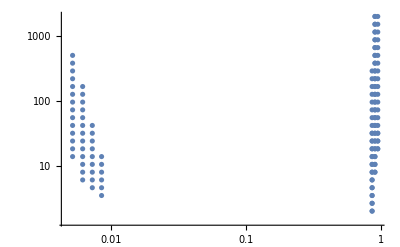

```mathematica
ListLogLogPlot[corrdataclass[[1,14]][["data"]]/.LF[a__]:>{{a}[[1]],{a}[[2]] }]
```

```mathematica
corrdataclass[[1,14]][["data"]]
```

```mathematica
(*
testcorrplot=
Table[
flavour=0;
x=fxQgrid2class[[flavour+6]][["data"]][[igrid]][[1]];Q=fxQgrid2class[[flavour+6]][["data"]][[igrid]][[2]];
corrxQ=pdfHessianCorrelationfake[
fxQgrid2class[[flavour+6]][["data"]][[600]]/.LF[a__]:>Drop[{a},2],
fxQgrid2class[[flavour+6]][["data"]][[igrid]]/.LF[a__]:>Drop[{a},2]
];
(*LF[x,Q,corrxQ]*)If[Abs[corrxQ]>0.5,{x,Q},{0.99,2}](*corrxQ*),
{igrid,1,Datamethods[["getNpt"]][fxQgrid2class[[flavour+6]] ]}
]
*)
```

```mathematica
ListLogLogPlot[testcorrplot]
```

```mathematica
obsgridLFdata[[1,1]]
```

{{LF[0.00001,2.,0.105024,-0.470009,0.495218,0.,0.],LF[0.0000213812,2.,0.105024,-0.470009,0.495218,0.,0.],2102,LF[0.944111,2000.,0.105024,-0.470009,0.495218,0.00362033,0.00731058],LF[0.99,2000.,0.105024,-0.470009,0.495218,1.07087×10^-7,2.16241×10^-7]},3,{1}}
 |  |  |  |

```mathematica
Select[obsgridLFdata[[1,8+6,4]],Abs[#[[7]] ]≥0.7&]
```

{LF[0.944111,18.2402,0.116509,0.643966,0.394727,0.305936,0.775056],LF[0.944111,24.0453,0.116509,0.643966,0.394727,0.311231,0.788471],LF[0.899835,31.6979,0.116509,0.643966,0.394727,0.27693,0.701573],LF[0.944111,31.6979,0.116509,0.643966,0.394727,0.316315,0.801351],LF[0.899835,41.7859,0.116509,0.643966,0.394727,0.278595,0.70579],LF[0.944111,41.7859,0.116509,0.643966,0.394727,0.321006,0.813234],LF[0.899835,55.0846,0.116509,0.643966,0.394727,0.280172,0.709785],LF[0.944111,55.0846,0.116509,0.643966,0.394727,0.325119,0.823655],LF[0.899835,72.6156,0.116509,0.643966,0.394727,0.281686,0.713621],LF[0.944111,72.6156,0.116509,0.643966,0.394727,0.325889,0.825607],LF[0.899835,95.726,0.116509,0.643966,0.394727,0.283126,0.717269],LF[0.944111,95.726,0.116509,0.643966,0.394727,0.326474,0.827087],LF[0.899835,126.191,0.116509,0.643966,0.394727,0.284482,0.720706],LF[0.944111,126.191,0.116509,0.643966,0.394727,0.326993,0.828403],LF[0.944111,166.353,0.116509,0.643966,0.394727,0.327454,0.829571],LF[0.944111,219.296,0.116509,0.643966,0.394727,0.327864,0.83061],LF[0.944111,289.088,0.116509,0.643966,0.394727,0.328255,0.831599],LF[0.944111,381.092,0.116509,0.643966,0.394727,0.328603,0.83248],LF[0.944111,502.377,0.116509,0.643966,0.394727,0.328907,0.833252],LF[0.944111,662.262,0.116509,0.643966,0.394727,0.329201,0.833996],LF[0.944111,873.032,0.116509,0.643966,0.394727,0.329466,0.834668],LF[0.944111,1150.88,0.116509,0.643966,0.394727,0.317761,0.805014],LF[0.944111,1517.16,0.116509,0.643966,0.394727,0.31714,0.803441],LF[0.944111,2000.,0.116509,0.643966,0.394727,0.31659,0.802048]}